```mathematica
Protect[A,b,c,f,s,n,ψ,φ];
NR=SetPrecision;
DomainOptimizedSF[s_Integer,α_,Nacc_: 60]:=Block[{int,int0,INT,param,ρ,m,n,i,j,nA,nb,a,p,k,A,b},p=1;
int=Integrate[p ρ^n Cos[m φ],{ρ,0,1},{φ,π-α,π+α},Assumptions->{n∈Integers,n≥0}];
int0=Integrate[p ρ^n,{ρ,0,1},{φ,π-α,π+α},Assumptions->{n∈Integers,n≥0}];
INT[i_,j_]:=If[i==j,int0/.{n->(i+j)},int/.{n->i+j,m->i-j}];
A=Table[INT[i,j],{i,1,s},{j,1,s}];
b=Table[INT[i,0],{i,1,s}];
{nA,nb}=NR[#,Nacc]&/@{A,b};
a=LinearSolve[nA,-nb];
Evaluate[(1+Table[#^i,{i,s}].a)]&]

ArcOptimizedSF[s_Integer,α_,Nacc_: 60]:=Block[{int,INT,param,ρ,m,n,i,j,nA,nb,a,p,k},int=Integrate[ρ^m Cos[n (π-α)],{ρ,0,1},Assumptions->{m∈Integers,n∈Integers,m≥0}]+If[n==0,π/2,Evaluate[Integrate[Cos[n φ],{φ,π-α,π},Assumptions->{n∈Integers}]]];
INT[i_,j_]:=int/.{m->i+j,n->i-j};
A=Table[INT[i,j],{i,1,s},{j,1,s}];
b=Table[INT[i,0],{i,1,s}];
{nA,nb}=NR[#,Nacc]&/@{A,b};
a=LinearSolve[nA,-nb];
Evaluate[(1+Table[#^i,{i,s}].a)]&];

GetCompositeERK[R_]:=Block[{roots,imz,rez,LebedevParam,z,Rz},Rz=R[z];
If[Exponent[Rz,z]==1,Return[{s->1,A->{{}},b->{R[1]-1}}];];
roots=(List@@Roots[Rz==0,z])[[All,2]];
(*Print[roots];*)(*imz=(Cases[roots,_Complex]//Sort)~Partition~2;*)imz=(Select[roots,!(N[#]∈Reals)&]//Sort)~Partition~2;
rez=Select[roots,N[#]∈Reals&];
rez=If[!OddQ@Length@rez,Partition[rez,2],Partition[rez,2]~Join~{rez[[-1]]}];
(*Print[rez,imz];*)LebedevParam[{z1_,z2_}]:=Block[{δ1,δ2,α,β,γ},(*roots=If[S>1,(List@@Roots[Rz==0,z])[[All,2]],{-1}];*){δ1,δ2}=-1/{z1,z2};
α=(δ1+δ2)/2//Re;
γ=(1-(δ1 δ2)/α^2)//Re;
β={α (1+γ),α (1-γ)};
{s->2,A->{{α//Simplify}},b->β//Simplify}];
LebedevParam[z_]:={s->1,A->{{1.}},b->{-(1/z)}};
LebedevParam/@(imz~Join~rez)];

ApplyRK[RK_,M_,bb_,y_,ω_]:=Block[{A,b,s,k={}},RK/.Rule->Set;
Do[
AppendTo[k,-bb+M.(y+ω Sum[A[[i-1,j]] k[[j]],{j,1,i-1}])],{i,1,s}];
y+ω b.k];

ApplyRKAll[RKS_,M_,bb_,y0_,ω_]:=Block[{y=y0},Scan[(y=ApplyRK[#,M,bb,y,ω])&,RKS];
y];
```

```mathematica
getMinIndex[A_]:=Block[{i,j, minVal=Norm[A⟦1⟧],minInd=1},For[i=1, i≤Length[A],i++,
If[Norm[A⟦i⟧]<minVal,
minVal=Norm[A⟦i⟧];
minInd=i;
];
];
Return[i];
];
getMaxIndex[A_]:=Block[{i,j, maxVal=Norm[A⟦1⟧],maxInd=1},For[i=1, i≤Length[A],i++,
If[Norm[A⟦i⟧]>maxVal,
maxVal=Norm[A⟦i⟧];
maxInd=i;
];
];
Return[i];
];
sumByRow=Sum[Abs[#⟦i⟧],{i,1,Length[#]}]&;
```

```mathematica
quantilsList=Table[Quantile[diffList⟦1⟧,0.1 i],{i, 1,10}];
relMatrix=Table[If[quantilsList⟦k⟧>0,quantilsList⟦j⟧/quantilsList⟦k⟧,0],{j,1,Length[quantilsList]-1},{k,1,Length[quantilsList]-1}];
badQuantil=getMinIndex[Transpose[relMatrix]];
```

```mathematica
R2=DomainOptimizedSF[10,π/3];
RKS=GetCompositeERK[R2];
```

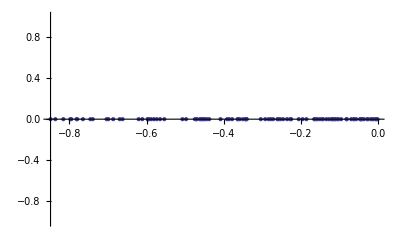

1578.46

```mathematica
NN=50;
eigenvalues=Table[-i^3,{i,1,NN}];
timesList=Table[If[i<15,3,1],{i,1,NN}];

diagArray={};
subDiagArray={};

For[i=1,i≤Length[eigenvalues],i++,
For[j=1,j≤timesList⟦i⟧,j++,
AppendTo[diagArray,eigenvalues⟦i⟧];
];
For[j=1,j≤timesList⟦i⟧-1,j++,
AppendTo[subDiagArray,1];
];
If[i≠Length[eigenvalues],
AppendTo[subDiagArray,0];
];

];

evMatrix=DiagonalMatrix[diagArray]+DiagonalMatrix[subDiagArray,-1];
complexSpectrumMatrix={{1,-2},{2,1}};
(*AAA=KroneckerProduct[complexSpectrumMatrix,evMatrix];*)
AAA=-ExampleData[{"Matrix","HB/nos4"}];
initialMatrix=AAA;
eigenvalues=Eigenvalues[AAA];
ListPlot[{Re[#],Im[#]}&/@eigenvalues]

NN=Length[AAA];
exactSolution=Table[1,{i,1,NN}];
initialRP=AAA.exactSolution;
bbb=initialRP;
y0=Table[100 ,{i,1,NN}];
ω=0.7*1./Max[Abs[eigenvalues]];

Gxb=AAA.#-bbb&;
diffList={};
discontinuityList={};
yList={};
hS=Table[0,{i,1,NN}];
coef=1.;
quantilsCnt=3;
componentEqualTozero=0.0001;
Print[Max[Abs[eigenvalues]]/Min[Abs[eigenvalues]]];
```

```mathematica
iterCount =1;
interParm=2000;
quantileNumber=1;
```

```mathematica
For[i=1, i<=300,i++,
rCurrentStep=Gxb[y0];
y1=ApplyRKAll[RKS,AAA,bbb,y0,ω];
AppendTo[yList,y1];
rNextStep=Gxb[y1];
diff=Abs[rCurrentStep-rNextStep];
AppendTo[discontinuityList,rNextStep];
AppendTo[diffList,diff];
(*Print["rNextStep",rNextStep];*)
maxDiff=Max[diff];

(*Print["diff", diff];
Print["Median",Median[diff], " average"];*)
quantilsList=Table[Quantile[diff,1/quantilsCnt ii],{ii, 1,quantilsCnt}];

relationDiffs=Table[diffList⟦1⟧⟦j⟧/If[diff⟦j⟧>0.,diff⟦j⟧,0.000001],{j,1,NN}];
(*Print["relationDiffs",relationDiffs];*)
relationDiffsquantilsList=Table[Quantile[relationDiffs,1/quantilsCnt ii],{ii, 1,quantilsCnt}];
zList=Table[If[quantilsList⟦quantileNumber⟧>diff⟦j⟧&&relationDiffsquantilsList⟦quantileNumber⟧>relationDiffs⟦j⟧&&Abs[rNextStep⟦j⟧]>componentEqualTozero,Min[coef quantilsList⟦1⟧/diff⟦j⟧,1.1],1],{j,1,NN}];

z=DiagonalMatrix[zList];
(*Print[Eigenvalues[AAA]];*)
spectrRadiousEstimation=Min[Max[sumByRow/@AAA],Max[sumByRow/@Transpose[AAA]]];
ω=0.7/spectrRadiousEstimation;
(*Print["Answer:",y1];*)
y0=y1;
iterCount++;
If[iterCount>interParm,
AAA=z.AAA;
bbb=z.bbb;
Print["!!!!!"];
Print[zList];
Print["Omega:",ω];
Print["Spectr Condition Number",Max[Abs[Eigenvalues[AAA]]]/Min[Abs[Eigenvalues[AAA]]] ];
Print["\n"];
iterCount=0;

];



]
```

```mathematica
precondEqSolution=y0;
initEqSolution=y0;
precondOmega=ω;
initOmega=0.7*1./Min[Max[sumByRow/@initialMatrix],Max[sumByRow/@Transpose[initialMatrix]]];

For[j=1,j<1000,j++,
precondEqSolution=ApplyRKAll[RKS,AAA,bbb,precondEqSolution,precondOmega];
initEqSolution=ApplyRKAll[RKS,initialMatrix,initialRP,initEqSolution,initOmega];
]
precondEqSolution;
initEqSolution;

Norm[precondEqSolution-exactSolution ]
Norm[initEqSolution-exactSolution ]
```

1.76257

1.34689

```mathematica
Max[Abs[Eigenvalues[AAA]]]
Max[Abs[Eigenvalues[initialMatrix]]]
```

0.851733

0.849138

```mathematica
Import["ExampleData/matrces"]
```

```mathematica
ExampleData["Matrix"]
```

```mathematica
Transpose[Last[JordanDecomposition[matrix]]]//MatrixForm
```